```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]
workingdirectory=$HomeDirectory<>"/kette_repo/ComptonLIT/mul_helion_par/results/";
SetDirectory[workingdirectory]
basisdims=Sort[DeleteDuplicates[ToExpression[StringSplit[#,"-"][[-1]]]&/@Select[FileNames[],StringTake[#,Min[3,StringLength[#]]]=="LIT"&]]]

ℏc=197.32858;
Mnucl=(938.2796+939.5731)/2.;
multipolarity=1;
parity="-";
J=0.5;
mJ=0.5;
σI=5;
threshold=10^-8;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
```

/home/kirscher/kette_repo/ComptonLIT/mul_helion_par/results

{48,96,144,192,240,288,336,384,432,468,504,540,576,612,648,684,720,756,792,828,864,900,936,972,1008,1038,1068,1074,1110,1146,1182,1218}

```mathematica
LITs={};
For[dd=1,dd≤Length[basisdims],dd++,
lbd=basisdims[[dd]];
NormHamMat=ReadList["./norm-ham-litME-"<>ToString[J]<>"^"<>parity<>"_1-"<>ToString[lbd],Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
genevham=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
normev=Sort[Eigenvalues[norm],Re[#1]>Re[#2]&];

Print["JbasisDim = ",JbasisDim];
file="./LIT_SOURCE_"<>ToString[J]<>"^"<>parity<>"_mJ"<>ToString[mJ]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[JbasisDim];
Print[file];
inhomo=ReadList[file,Real,RecordLists->True][[-1]];(*use largest photon momentum as test default*)

renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];

ham=renorm.ham.renorm;norm=renorm.norm.renorm;
inhomoN=renorm.inhomo;
genevhamN=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
normevN=Sort[Eigenvalues[norm],Re[#1]>Re[#2]&];
pseudoinverse[threshold_,σR_,σI_]:=Block[{Mm=ham-(σR-σI ⅈ) norm},
PseudoInverse[Mm,Tolerance->threshold]];
thresholds=N[{threshold}];
AppendTo[LITs,((Function[{σR},Block[{mm,coeff},mm=pseudoinverse[#,σR,σI];coeff=mm.inhomo;{σR,Chop[Conjugate[coeff].norm.coeff]}]]/@σRs)&/@thresholds)[[1]]];
]
```

JbasisDim = 48

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-48

JbasisDim = 96

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-96

JbasisDim = 144

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-144

JbasisDim = 192

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-192

JbasisDim = 240

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-240

JbasisDim = 288

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-288

JbasisDim = 336

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-336

JbasisDim = 384

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-384

JbasisDim = 432

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-432

JbasisDim = 468

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-468

JbasisDim = 504

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-504

JbasisDim = 540

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-540

JbasisDim = 576

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-576

JbasisDim = 612

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-612

JbasisDim = 648

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-648

JbasisDim = 684

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-684

JbasisDim = 720

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-720

JbasisDim = 756

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-756

JbasisDim = 792

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-792

JbasisDim = 828

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-828

JbasisDim = 864

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-864

JbasisDim = 900

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-900

JbasisDim = 936

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-936

JbasisDim = 972

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-972

JbasisDim = 1008

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-1008

JbasisDim = 1038

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-1038

JbasisDim = 1068

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-1068

JbasisDim = 1074

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-1074

JbasisDim = 1110

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-1110

JbasisDim = 1146

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-1146

JbasisDim = 1182

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-1182

JbasisDim = 1218

./LIT_SOURCE_0.5^-_mJ0.5_MUL1_bv_1-1218

```mathematica
Length[LITs]
```

32

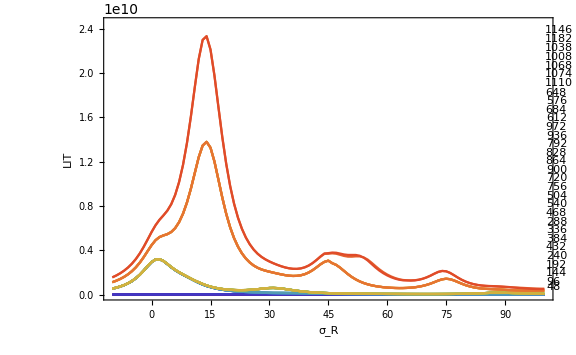

```mathematica
pltmaxcfg=31;
peakmax=Max[Table[Max[Re[LITs[[nn]]][[;;,2]]],{nn,pltmaxcfg}]];
ListPlot[Re[LITs[[;;pltmaxcfg]]],Joined->True,Frame->True,PlotRange->{{σRs[[1]],σRs[[-1]]},{0,1.05 peakmax}},FrameLabel->{"σ_R","LIT"}, PlotStyle->Table[ColorData["Rainbow"][N[FractionalPart[(i-1)/Length[basisdims]]]]&[Floor[i-1,1]+1],{i,1,Length[basisdims]}],PlotLabels->Placed[basisdims,Automatic],ImageSize->Large]
```

#### Alternative approach (norm zero-mode removal)

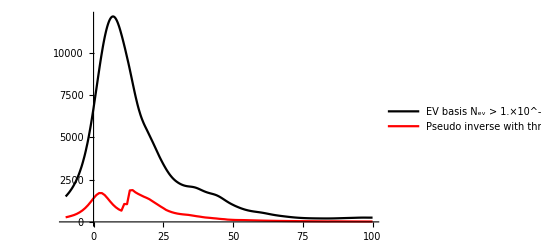

```mathematica
lbd=basisdims[[pltmaxcfg]];
NormHamMat=ReadList["./norm-ham-litME-"<>ToString[J]<>"^"<>parity<>"_1-"<>ToString[lbd],Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
file="./LIT_SOURCE_"<>ToString[J]<>"^"<>parity<>"_mJ"<>ToString[mJ]<>"_MUL"<>ToString[multipolarity]<>"_bv_1-"<>ToString[JbasisDim];
inhomo=ReadList[file,Real,RecordLists->True][[-1]];(*use largest photon momentum as test default*)
Clear[normreg];normreg[threshold_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{μs,Or}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]<=threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}]
Clear[decompose];decompose[threshold_,pr_:False,debug_:False]:= Block[{Oμ,Or,μs,oλs,otrf},{Oμ,Or,μs}=normreg[threshold];If[debug,Print[MatrixForm[Chop[(Transpose[Oμ].norm).Oμ]]]];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];If[pr,Print["overlap of ψ with norm zero modes (norm, overlap)\n",MatrixForm[Transpose[{μs,Or.inhomo}]]]];{λs,trf.(Transpose[Oμ].inhomo)}]
litcomp[threshold_]:=Block[{λscf=Transpose[decompose[threshold]]},Plus@@(((#[[2]])^2/((#[[1]]-σRe)^2+σIm^2))&/@λscf)]
litshow[threshold_]:=Block[{λscf=Transpose[decompose[threshold]]},{#[[1]],Abs[#[[2]]]^2}&/@λscf]
th=10^-6;
Show[
Plot[Evaluate[litcomp[th]/.σIm->σI],{σRe,-10,100},
PlotLegends->{"EV basis N_ev > "<>ToString[N[th],TraditionalForm]},PlotStyle->{Thick,Black}],
ListLinePlot[Function[{σR},Block[{mm,coeff},mm=pseudoinverse[th,σR,σI];coeff=mm.inhomo;{σR,Re[Conjugate[coeff].norm.coeff]}]]/@σRs,PlotRange->All,PlotStyle->Red,PlotLegends->{"Pseudo inverse with thres = "<>ToString[N[th],TraditionalForm]}]
]
```

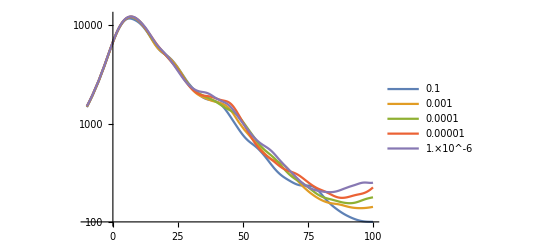

```mathematica
thresholds={0.1,0.001,0.0001,0.00001,0.000001};
LogPlot[Evaluate[((f=litcomp[#]/.σIm->σI)&/@thresholds)],{σRe,-10,100},PlotLegends->thresholds]
```

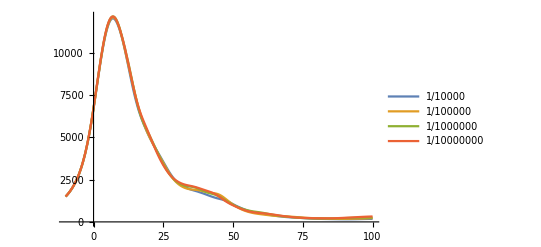

```mathematica
thresholds={10^-4,10^-5,10^-6,10^-7};
Plot[Evaluate[((f=litcomp[#]/.σIm->σI)&/@thresholds)],{σRe,-10,100},PlotLegends->thresholds]
```

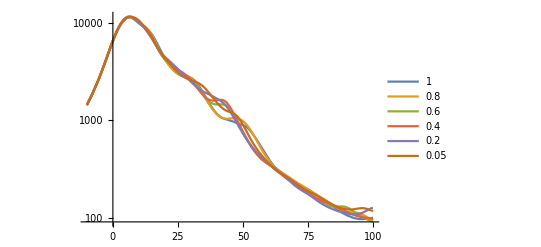

```mathematica
thresholds={1,0.8,0.6,0.4,0.2,0.05};
LogPlot[Evaluate[((f=litcomp[#]/.σIm->σI)&/@thresholds)],{σRe,-10,100},PlotRange->All,PlotLegends->thresholds]
```

```mathematica
Table[inhomo.PseudoInverse[norm,Tolerance->10^-n].inhomo,{n,10,0,-1}]
```

{69040.9,68369.1,67193.3,65468.7,64304.4,61086.2,57317.4,51177.5,25049.9,303.408,1.60484}

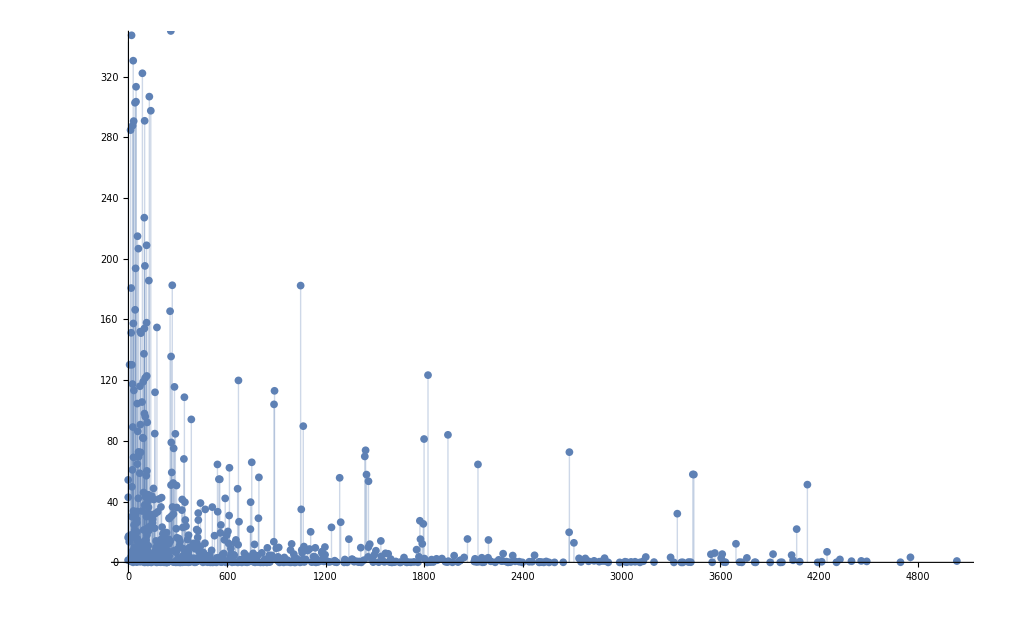

```mathematica
ListPlot[litshow[10^-4],Filling->Axis]
```